This notebook generates Local Chern Number of the BHZ model (Quantum Anomalous Hall Insulator (QAHI)) on a square lattice, and exports them to a .dat file

The .dat files generated with this notebook can be visualized with Make_Plots_Local_Chern_Number_squarelattice.nb

```mathematica
tstart = AbsoluteTime[];
```

```mathematica
L=60
```

60

```mathematica
Clear[Lx,Ly,A,m,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons,P,Q,FilledEigenvectors,ValAHIRange,ValVecNor,
XList,XListKron,YList,YListKron,X1,Y1,ChernMatrix,ChernMatrixDiagonalList,ChernMatrixSiteWiseList]
```

```mathematica
(** The model is, H = t (SinKx σx + SinKy σy) -(m - 2 t0 (2 - CosKx - CosKy))σz **)
```

```mathematica
(** Change Lx, Ly and m in the following lines before running the code **)
```

```mathematica
Lx=L;
Ly=L;
A=Lx*Ly;
```

```mathematica
(** we will set t = 2 t0 = 1. **)
```

```mathematica
t=1
t0 = 0.5;
m = 3* t0;
```

```mathematica
(** Here we create the hopping matrices **)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(** Define the Hamiltonian **)
```

```mathematica
(** PBC is α = 1, OBC is α = 0 **)
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP,σ2])-KroneckerProduct[m*Cons-2t0*(2* Cons -CX2D-CY2D-α*CX2DP-α*CY2DP),σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValAHIRange]
```

```mathematica
(** The calculation works for both PBC and OBC, but here we use PBC **)
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHI[t,t0,m,1]];
```

```mathematica
ValAHIRange=Table[val[[j]],{j,1,2 A}];
```

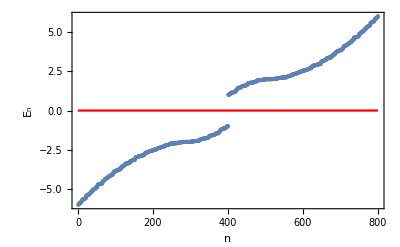

```mathematica
Show[ListPlot[Sort[val],Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
(**------------------- Real space Chern number calculation as per PHYSICAL REVIEW B 84,241106(R) (2011) -------------------**)
```

```mathematica
Clear[vecNormalized,ValVecNor,XList, YList, XListKron, YListKron,P]
```

```mathematica
vecNormalized=Table[Normalize[vec[[i]]],{i,1,2 A}];
```

```mathematica
ValVecNor=SortBy[Transpose[{val,vecNormalized}],First];
```

```mathematica
(** We generate a list of length Lx*Ly, which gives the X coordinate at site (x,y) **)
```

```mathematica
XList = Flatten[Transpose[Table[i,{i,1,Lx},{j,1,Ly}]]];
```

```mathematica
(** We generate a list of length Lx*Ly, which gives the Y coordinate at site (x,y) **)
```

```mathematica
YList = Flatten[Table[i,{i,1,Lx},{j,1,Ly}]];
```

```mathematica
(** To get the coordinates of the orbital, we repeat the coordinate, i.e., instead of {1,2,3,...} we generate {1,1,2,2,3,3,...} **)
```

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(** We work with the half filled limit, and collect the filled eigenvectors **)
```

```mathematica
FilledEigenvectors = Table[ValVecNor[[i]][[2]],{i,1,A}];
```

```mathematica
(**-------Here we calculate the projection matrix P-------**)
```

```mathematica
P=Table[0,{i,1,2A},{j,1,2A}];
```

```mathematica
Dimensions[P]
```

{800,800}

```mathematica
Dimensions[TensorProduct[FilledEigenvectors[[1]] ,Conjugate[ FilledEigenvectors[[1]]]]]
```

{800,800}

```mathematica
Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i,1,A}]
```

```mathematica
(**-------Now we generate the X and Y operators in the Wannier basis-------**)
```

```mathematica
X1 = DiagonalMatrix[XListKron];
```

```mathematica
Y1 = DiagonalMatrix[YListKron];
```

```mathematica
Q = IdentityMatrix[2 A] - P;
```

```mathematica
(**-----Verify that Q.P = 0 upto numerical accuracy-----**)
```

```mathematica
Max[Abs[P.Q]]
```

3.17086×10^-15

```mathematica
(** Define the local Chern Operator in the Wannier basis **)
```

```mathematica
ChernMatrix=-4π Im[(P.X1.Q.Y1.P)];
```

```mathematica
(**-----The diagonal is the Wanneir orbitalwise list-----**)
```

```mathematica
ChernMatrixDiagonalList= Diagonal[ChernMatrix];
```

```mathematica
(** Here I add the contribution of both onsite orbitals to get sitewise local Chern number **)
```

```mathematica
ChernMatrixSiteWiseList = Table[ChernMatrixDiagonalList[[2 i]]+ChernMatrixDiagonalList[[2i-1]],{i,1,A}];
```

```mathematica
(**------------------------Here I export the list------------------------**)
```

```mathematica
Clear[location,filename,filenameString1,filenameString2,filenameString3]
```

```mathematica
location="data/";
```

```mathematica
filenameString1 = "datalocalChernLx=";
filenameString2="Ly=";
filenameString3 = "mbyt0=";
```

```mathematica
filename = StringJoin[location,filenameString1,ToString[Lx],filenameString2,ToString[Ly],filenameString3,ToString[m],".dat"]
```

```mathematica
Export[filename,ChernMatrixSiteWiseList];
```

```mathematica
(**----------------Here we generate some Histograms and plots, but later we will properly analyze the data-----------------------**)
```

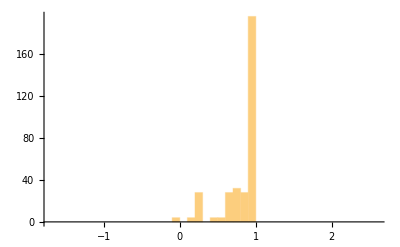

```mathematica
Histogram[ChernMatrixSiteWiseList]
```

```mathematica
(** Here we plot the on-site Chern number on every site. The periodicity of the plot is due to the edge effect. On the edges, the local Chern number deviates from its value at the bulk. **)
```

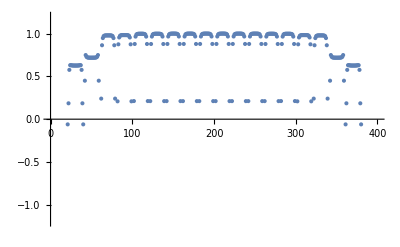

```mathematica
ListPlot[ChernMatrixSiteWiseList,PlotRange->{-1.2,1.2}]
```

```mathematica
tstop = AbsoluteTime[];
```

```mathematica
TimeTakenInSeconds = tstop - tstart
```

33.21107